```mathematica
b=2;
A=3;
```

{6.50266,Null}

{6.70671,Null}

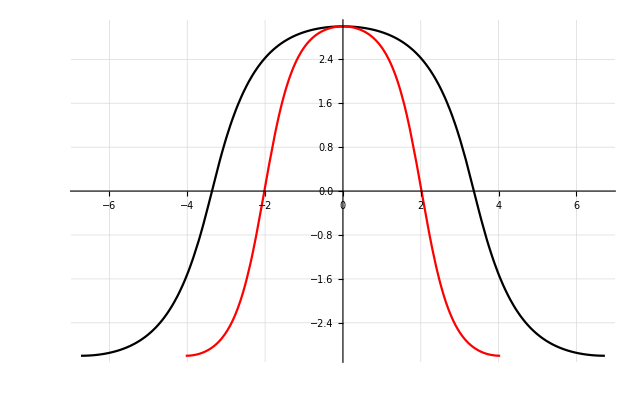

```mathematica
FSG[alpha_,A_]:=NIntegrate[1/Sqrt[2*(Cos[x]-Cos[A])],{x,A,alpha},MaxRecursion->1000];
listSG=Table[{FSG[alpha,A]/b,alpha},{alpha,-A,A,0.005}];//Timing//Quiet
listSG=Union[listSG,Reverse[Map[{-#[[1]],#[[2]]}&,listSG]]];
funSG=Interpolation[listSG,InterpolationOrder->2];
FGSG[alpha_,alpha0_]:=NIntegrate[1/Sqrt[-Sqrt[1+b^2*(1-Cos[x])]+Sqrt[1+b^2*(1-Cos[alpha0])]],{x,alpha0,alpha},MaxRecursion->1000];
listGSG=Table[{FGSG[alpha,A]/2,alpha},{alpha,-A,A,0.005}];//Timing//Quiet
listGSG=Union[listGSG,Reverse[Map[{-#[[1]],#[[2]]}&,listGSG]]];
funGSG=Interpolation[listGSG,InterpolationOrder->2];
p1=Plot[funGSG[t],{t,Min[listGSG[[All,1]]],Max[listGSG[[All,1]]]},PlotStyle->Black];
p2=Plot[funSG[t],{t,Min[listSG[[All,1]]],Max[listSG[[All,1]]]},PlotStyle->Red];
Show[p1,p2,GridLines->Automatic]
```